```mathematica
观察过渡过程
```

```mathematica
修改以下程序中的α即可
```

General::obspkg: "Statistics`NormalDistribution`" is now obsolete. The legacy version being loaded may conflict with current Mathematica functionality. See the Compatibility Guide for updating information.

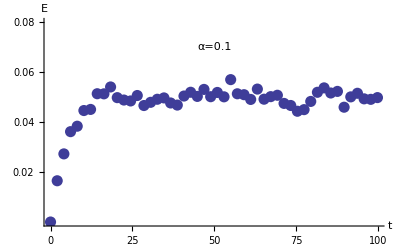

```mathematica
<<Statistics`NormalDistribution`
dis=NormalDistribution[0,1];
n=500;α=0.1;
m=1000;δt=0.1;time=(m-1)*δt;
fr=Table[Random[dis] √α,{i,n},{j,m}];
fr=Table[{δt*(i-1),fr[[j,i]]},{j,n},{i,m}];
fr=Table[Interpolation[fr[[i]]],{i,n}];
equ=Table[{x''[t]+α*x'[t]==fr[[i]][t],
x[0]==0,x'[0]==0},{i,n}];
s=Table[NDSolve[equ[[i]],x,{t,0,time},
MaxSteps->∞],{i,n}];
s=Flatten[s];
sample=50;δt=time/(sample-1);result={};
Do[section=Table[x'[δt*(i-1)]/.s[[j]],{j,n}];
AppendTo[result,
{δt*(i-1),Sum[section[[j]]^2,{j,n}]/n}],
{i,sample}]
ListPlot[result,PlotStyle->PointSize[0.02],
PlotRange->{0,0.08},AxesLabel->{"t","E"},
Ticks->{Automatic,0.02Range[4]},Epilog->Text["α="<>ToString[α],{50,0.07}]]
Clear[dis,n,m,δt,time,α,equ,fr,s,sample,
result,section,x]
```

```mathematica
α=0的情况
```

General::obspkg: "Statistics`NormalDistribution`" is now obsolete. The legacy version being loaded may conflict with current Mathematica functionality. See the Compatibility Guide for updating information.

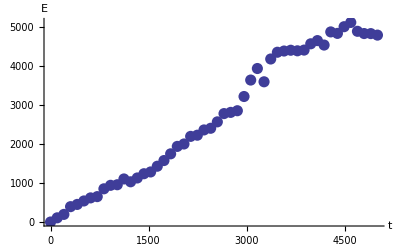

```mathematica
<<Statistics`NormalDistribution`
dis=NormalDistribution[0,1];
n=50;α=0;
m=5000;δt=1;time=(m-1)*δt;
fr=Table[Random[dis] ,{i,n},{j,m}];
fr=Table[{δt*(i-1),fr[[j,i]]},{j,n},{i,m}];
fr=Table[Interpolation[fr[[i]]],{i,n}];
equ=Table[{x''[t]+α*x'[t]==fr[[i]][t],
x[0]==0,x'[0]==0},{i,n}];
s=Table[NDSolve[equ[[i]],x,{t,0,time},
MaxSteps->∞],{i,n}];
s=Flatten[s];
sample=50;δt=time/(sample-1);result={};
Do[section=Table[x'[δt*(i-1)]/.s[[j]],{j,n}];
AppendTo[result,
{δt*(i-1),Sum[section[[j]]^2,{j,n}]/n}],
{i,sample}]
ListPlot[result,PlotStyle->PointSize[0.02],
PlotRange->All,AxesLabel->{"t","E"}]
Clear[dis,n,m,δt,time,α,equ,fr,s,sample,
result,section,x]
```

```mathematica
验证α=0时位移平凡的均值与时间的立方成正比
```

General::obspkg: "Statistics`NormalDistribution`" is now obsolete. The legacy version being loaded may conflict with current Mathematica functionality. See the Compatibility Guide for updating information.

0.0383587 t^3

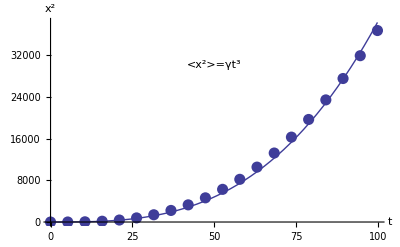

```mathematica
<<Statistics`NormalDistribution`
dis=NormalDistribution[0,1];
n=100;m=1000;δt=0.1;time=(m-1)*δt;α=0;
fr=Table[Random[dis] ,{i,n},{j,m}];
fr=Table[{δt*(i-1),fr[[j,i]]},{j,n},{i,m}];
fr=Table[Interpolation[fr[[i]]],{i,n}];
equs=
Table[{x''[t]+α*x'[t]==fr[[i]][t],x[0]==0,
x'[0]==0},{i,n}];
s=Table[NDSolve[equs[[i]],x,{t,0,time},
MaxSteps->∞],{i,n}];
s=Flatten[s];
sample=20;δt=time/(sample-1);result={};
Do[section=Table[x[δt*(i-1)]/.s[[j]],{j,n}];
AppendTo[result,
{δt*(i-1),Sum[section[[j]]^2,{j,n}]/n}],
{i,sample}]
fit=Fit[result,t^3,t]
g1=Plot[fit,{t,0,time},DisplayFunction->Identity];
g2=ListPlot[result,PlotStyle->PointSize[0.02],DisplayFunction->Identity];
Show[{g1,g2},DisplayFunction->$DisplayFunction,
AxesLabel->{"t","x^2"},Epilog->Text["<x^2>=γt^3",{50,30000}]]
Clear[dis,n,m,δt,time,α,equs,fr,s,result,section,x,fit,g1,g2]
```